```mathematica
ClearAll["Global'*"]
surfaceImage=-Graphics-;
(*surfaceImage=ImageCrop[surfaceImage,{crop_x,crop_y}];*)
Manipulate[{z=FillingTransform[ColorNegate[Binarize[surfaceImage,BinarizeSelector]]];

If[ShowBlackAndColorizedImage,z,"Disabled"],

distTrans=DistanceTransform[z,Padding->0];
marker=MaxDetect[ImageAdjust[distTrans],MarkerSelector];
WatershedImage=WatershedComponents[GradientFilter[z,GradientFilterSelector],marker,Method->"Rainfall"];
  If[ShowBlackAndColorizedImage,Colorize[WatershedImage],Colorize[WatershedImage];"Disabled"],
objects=SelectComponents[WatershedImage,"Count",SmallBodiesSizeSelector<#<BigBodiesSizeSelector&];
measures=ComponentMeasurements[objects,{"Centroid","EquivalentDiskRadius","Label"}];


measuresParam=ComponentMeasurements[objects,"Area"][[All,2]];
measuresParam=measuresParam*400/3600 (*Scaling*);
meanmeasuresParam=Mean[measuresParam];
combined=MapThread[{#1,#2}&,{Array[#&,Length[measuresParam]],measuresParam}];
combinedMean=combined;
combinedMean[[All,2]]=meanmeasuresParam;

Show[z,surfaceImage,Graphics[{Red,Thickness[0.01], Circle@@#&/@(measures[[All,2,1;;2]]),MapThread[Text[Style[#1,16],#2+{0.0(*Shift of Circle Labels*),0.0}]&,{measures[[All,2,3]],measures[[All,2,1]]}]}]],

If[Length[combined]>1,ListPlot[{combined,combinedMean},Joined->{False,True},AxesOrigin->{0,0},AxesLabel->{"particle number","Parameter"},Filling->{1->{2}}]],

measures//Length

},Column[{Row[{Control[{BinarizeSelector,0,1,.001}],Control[{SmallBodiesSizeSelector,1,500,10}],Control[{BigBodiesSizeSelector,300,50000,50}]}],

Row[{Control[{MarkerSelector,0.0001,1,.001}],Control[{GradientFilterSelector,.1,10,.02}],Control[{ShowBlackAndColorizedImage,{True,False}}]}]

  }] ]
```

Binarize::imginv: Expecting an image or graphics instead of surfaceImage.

ColorNegate::imginv: Expecting an image or graphics instead of Binarize[surfaceImage, 0.392].

FillingTransform::imginv: Expecting an image or graphics instead of ColorNegate[Binarize[surfaceImage, 0.392]].

DistanceTransform::imginv: Expecting an image or graphics instead of FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]].

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0].

MaxDetect::arg1: -- Message text not found -- (ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]])

GradientFilter::arg1: The first argument FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]] is neither a rectangular array nor an image.

WatershedComponents::imginv: Expecting an image or graphics instead of GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24].

Colorize::invinput: Expecting an integer matrix or an image instead of WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]], 0.0001], Method → "Rainfall"].

SelectComponents::invarg1: Expecting a valid label matrix or an image instead of WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]], 0.0001], Method → "Rainfall"].

ComponentMeasurements::invarg1: Expecting a valid label matrix, an image, or a list of an image and a label matrix instead of SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &].

General::stop: Further output of ComponentMeasurements :: invarg1 will be suppressed during this calculation.

Part::partd: Part specification ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[« 2 »]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[« 1 »], Rule[« 2 »]]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], "Area"] ⟦ All, 2 ⟧ is longer than depth of object.

MapThread::mptd: Object 1/9\ ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[« 1 »]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[« 2 »]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], "Area"] ⟦ All, 2 ⟧ at position {2, 2} in MapThread[{#1, #2} &, {{1, 2}, 1/9\ ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[« 2 »], MaxDetect[« 2 »], Rule[« 2 »]], "Count", Less[« 3 »] &], "Area"] ⟦ All, 2 ⟧}] has only 0 of required 1 dimensions.

Set::partw: Part 2 of {#1, #2} & does not exist.

Part::take: Cannot take positions 1 through 2 in "Count".

Part::pspec: Part specification Circle[1, 2] is neither a machine-sized integer nor a list of machine-sized integers.

Part::partd: Part specification ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[« 2 »]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[« 1 »], Rule[« 2 »]]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], {"Centroid", "EquivalentDiskRadius", "Label"}] ⟦ All, 2, 3 ⟧ is longer than depth of object.

Part::partd: Part specification ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[« 2 »]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[« 1 »], Rule[« 2 »]]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], {"Centroid", "EquivalentDiskRadius", "Label"}] ⟦ All, 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

MapThread::mptd: Object ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[« 2 »]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[« 1 »], Rule[« 2 »]]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], {"Centroid", "EquivalentDiskRadius", "Label"}] ⟦ All, 2, 3 ⟧ at position {2, 1} in Text[StyleBox[ has only 0 of required 1 dimensions.

Show::gcomb: Could not combine the graphics objects in FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392`]]], surfaceImage, GraphicsBox[List[RGBColor[1, 0, 0], Thickness[0.01`], Part[Circle[SelectComponents[WatershedComponents[GradientFilter[Skeleton[2]], MaxDetect[Skeleton[2]], Rule[Skeleton[2]]], .

MapThread::mptd: Object ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[« 2 »]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[« 1 »], Rule[« 2 »]]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], {"Centroid", "EquivalentDiskRadius", "Label"}] ⟦ All, 2, 3 ⟧ at position {2, 1} in Text[StyleBox[ has only 0 of required 1 dimensions.

General::stop: Further output of MapThread :: mptd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392`]]], surfaceImage, GraphicsBox[List[RGBColor[1, 0, 0], Thickness[0.01`], Part[Circle[SelectComponents[WatershedComponents[GradientFilter[Skeleton[2]], MaxDetect[Skeleton[2]], Rule[Skeleton[2]]], .

DistanceTransform::imginv: Expecting an image or graphics instead of FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]].

General::stop: Further output of DistanceTransform :: imginv will be suppressed during this calculation.

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.].

MaxDetect::arg1: -- Message text not found -- (ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.]])

General::stop: Further output of MaxDetect :: arg1 will be suppressed during this calculation.

WatershedComponents::imginv: Expecting an image or graphics instead of GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24].

General::stop: Further output of WatershedComponents :: imginv will be suppressed during this calculation.

SelectComponents::invarg1: Expecting a valid label matrix or an image instead of WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.]], 0.0001], Method → "Rainfall"].

General::stop: Further output of SelectComponents :: invarg1 will be suppressed during this calculation.

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.].

General::stop: Further output of ImageAdjust :: imginv will be suppressed during this calculation.

Binarize::imginv: Expecting an image or graphics instead of surfaceImage.

ColorNegate::imginv: Expecting an image or graphics instead of Binarize[surfaceImage, 0.392].

FillingTransform::imginv: Expecting an image or graphics instead of ColorNegate[Binarize[surfaceImage, 0.392]].

DistanceTransform::imginv: Expecting an image or graphics instead of FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]].

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0].

MaxDetect::arg1: -- Message text not found -- (ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]])

GradientFilter::arg1: The first argument FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]] is neither a rectangular array nor an image.

WatershedComponents::imginv: Expecting an image or graphics instead of GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24].

Colorize::invinput: Expecting an integer matrix or an image instead of WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]], 0.0001], Method → "Rainfall"].

SelectComponents::invarg1: Expecting a valid label matrix or an image instead of WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]], 0.0001], Method → "Rainfall"].

ComponentMeasurements::invarg1: Expecting a valid label matrix, an image, or a list of an image and a label matrix instead of SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &].

Part::partd: Part specification ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[« 2 »]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[« 1 »], Rule[« 2 »]]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], "Area"] ⟦ All, 2 ⟧ is longer than depth of object.

MapThread::mptd: Object 1/9\ ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[« 1 »]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[« 2 »]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], "Area"] ⟦ All, 2 ⟧ at position {2, 2} in MapThread[{#1, #2} &, {{1, 2}, 1/9\ ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[« 2 »], MaxDetect[« 2 »], Rule[« 2 »]], "Count", Less[« 3 »] &], "Area"] ⟦ All, 2 ⟧}] has only 0 of required 1 dimensions.

Set::partw: Part 2 of {#1, #2} & does not exist.

Part::take: Cannot take positions 1 through 2 in "Count".

Part::pspec: Part specification Circle[1, 2] is neither a machine-sized integer nor a list of machine-sized integers.

Part::partd: Part specification ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[« 2 »]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[« 1 »], Rule[« 2 »]]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], {"Centroid", "EquivalentDiskRadius", "Label"}] ⟦ All, 2, 3 ⟧ is longer than depth of object.

Part::partd: Part specification ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[« 2 »]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[« 1 »], Rule[« 2 »]]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], {"Centroid", "EquivalentDiskRadius", "Label"}] ⟦ All, 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

MapThread::mptd: Object ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[« 2 »]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[« 1 »], Rule[« 2 »]]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], {"Centroid", "EquivalentDiskRadius", "Label"}] ⟦ All, 2, 3 ⟧ at position {2, 1} in Text[StyleBox[ has only 0 of required 1 dimensions.

Show::gcomb: Could not combine the graphics objects in FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392`]]], surfaceImage, GraphicsBox[List[RGBColor[1, 0, 0], Thickness[0.01`], Part[Circle[SelectComponents[WatershedComponents[GradientFilter[Skeleton[2]], MaxDetect[Skeleton[2]], Rule[Skeleton[2]]], .

DistanceTransform::imginv: Expecting an image or graphics instead of FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]].

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.].

MaxDetect::arg1: -- Message text not found -- (ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.]])

WatershedComponents::imginv: Expecting an image or graphics instead of GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24].

SelectComponents::invarg1: Expecting a valid label matrix or an image instead of WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.]], 0.0001], Method → "Rainfall"].

ComponentMeasurements::invarg1: Expecting a valid label matrix, an image, or a list of an image and a label matrix instead of SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &].

General::stop: Further output of ComponentMeasurements :: invarg1 will be suppressed during this calculation.

MapThread::mptd: Object 0.111111\ ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[« 1 »]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[« 2 »]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], "Area"] ⟦ All, 2 ⟧ at position {2, 2} in MapThread[{#1, #2} &, {{1., 2.}, 0.111111\ ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[« 2 »], MaxDetect[« 2 »], Rule[« 2 »]], "Count", Less[« 3 »] &], "Area"] ⟦ All, 2 ⟧}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread :: mptd will be suppressed during this calculation.

DistanceTransform::imginv: Expecting an image or graphics instead of FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]].

General::stop: Further output of DistanceTransform :: imginv will be suppressed during this calculation.

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.].

General::stop: Further output of ImageAdjust :: imginv will be suppressed during this calculation.

MaxDetect::arg1: -- Message text not found -- (ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.]])

General::stop: Further output of MaxDetect :: arg1 will be suppressed during this calculation.

WatershedComponents::imginv: Expecting an image or graphics instead of GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24].

General::stop: Further output of WatershedComponents :: imginv will be suppressed during this calculation.

SelectComponents::invarg1: Expecting a valid label matrix or an image instead of WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.]], 0.0001], Method → "Rainfall"].

General::stop: Further output of SelectComponents :: invarg1 will be suppressed during this calculation.

Binarize::imginv: Expecting an image or graphics instead of surfaceImage.

ColorNegate::imginv: Expecting an image or graphics instead of Binarize[surfaceImage, 0.392].

FillingTransform::imginv: Expecting an image or graphics instead of ColorNegate[Binarize[surfaceImage, 0.392]].

DistanceTransform::imginv: Expecting an image or graphics instead of FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]].

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0].

MaxDetect::arg1: -- Message text not found -- (ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]])

GradientFilter::arg1: The first argument FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]] is neither a rectangular array nor an image.

WatershedComponents::imginv: Expecting an image or graphics instead of GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24].

Colorize::invinput: Expecting an integer matrix or an image instead of WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]], 0.0001], Method → "Rainfall"].

SelectComponents::invarg1: Expecting a valid label matrix or an image instead of WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]], 0.0001], Method → "Rainfall"].

ComponentMeasurements::invarg1: Expecting a valid label matrix, an image, or a list of an image and a label matrix instead of SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &].

Part::partd: Part specification ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[« 2 »]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[« 1 »], Rule[« 2 »]]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], "Area"] ⟦ All, 2 ⟧ is longer than depth of object.

MapThread::mptd: Object 1/9\ ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[« 1 »]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[« 2 »]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], "Area"] ⟦ All, 2 ⟧ at position {2, 2} in MapThread[{#1, #2} &, {{1, 2}, 1/9\ ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[« 2 »], MaxDetect[« 2 »], Rule[« 2 »]], "Count", Less[« 3 »] &], "Area"] ⟦ All, 2 ⟧}] has only 0 of required 1 dimensions.

Set::partw: Part 2 of {#1, #2} & does not exist.

Part::take: Cannot take positions 1 through 2 in "Count".

Part::pspec: Part specification Circle[1, 2] is neither a machine-sized integer nor a list of machine-sized integers.

Part::partd: Part specification ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[« 2 »]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[« 1 »], Rule[« 2 »]]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], {"Centroid", "EquivalentDiskRadius", "Label"}] ⟦ All, 2, 3 ⟧ is longer than depth of object.

Part::partd: Part specification ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[« 2 »]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[« 1 »], Rule[« 2 »]]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], {"Centroid", "EquivalentDiskRadius", "Label"}] ⟦ All, 2, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

MapThread::mptd: Object ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[« 2 »]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[« 1 »], Rule[« 2 »]]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], {"Centroid", "EquivalentDiskRadius", "Label"}] ⟦ All, 2, 3 ⟧ at position {2, 1} in Text[StyleBox[ has only 0 of required 1 dimensions.

Show::gcomb: Could not combine the graphics objects in FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392`]]], surfaceImage, GraphicsBox[List[RGBColor[1, 0, 0], Thickness[0.01`], Part[Circle[SelectComponents[WatershedComponents[GradientFilter[Skeleton[2]], MaxDetect[Skeleton[2]], Rule[Skeleton[2]]], .

DistanceTransform::imginv: Expecting an image or graphics instead of FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]].

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.].

MaxDetect::arg1: -- Message text not found -- (ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.]])

WatershedComponents::imginv: Expecting an image or graphics instead of GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24].

SelectComponents::invarg1: Expecting a valid label matrix or an image instead of WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.]], 0.0001], Method → "Rainfall"].

ComponentMeasurements::invarg1: Expecting a valid label matrix, an image, or a list of an image and a label matrix instead of SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &].

General::stop: Further output of ComponentMeasurements :: invarg1 will be suppressed during this calculation.

MapThread::mptd: Object 0.111111\ ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[FillingTransform[ColorNegate[« 1 »]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[« 2 »]], 0.0001], Method → "Rainfall"], "Count", FE`SmallBodiesSizeSelector$$17 < #1 < FE`BigBodiesSizeSelector$$17 &], "Area"] ⟦ All, 2 ⟧ at position {2, 2} in MapThread[{#1, #2} &, {{1., 2.}, 0.111111\ ComponentMeasurements[SelectComponents[WatershedComponents[GradientFilter[« 2 »], MaxDetect[« 2 »], Rule[« 2 »]], "Count", Less[« 3 »] &], "Area"] ⟦ All, 2 ⟧}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread :: mptd will be suppressed during this calculation.

DistanceTransform::imginv: Expecting an image or graphics instead of FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]].

General::stop: Further output of DistanceTransform :: imginv will be suppressed during this calculation.

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.].

General::stop: Further output of ImageAdjust :: imginv will be suppressed during this calculation.

MaxDetect::arg1: -- Message text not found -- (ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.]])

General::stop: Further output of MaxDetect :: arg1 will be suppressed during this calculation.

WatershedComponents::imginv: Expecting an image or graphics instead of GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24].

General::stop: Further output of WatershedComponents :: imginv will be suppressed during this calculation.

SelectComponents::invarg1: Expecting a valid label matrix or an image instead of WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0.]], 0.0001], Method → "Rainfall"].

General::stop: Further output of SelectComponents :: invarg1 will be suppressed during this calculation.

Binarize::imginv: Expecting an image or graphics instead of surfaceImage.

ColorNegate::imginv: Expecting an image or graphics instead of Binarize[surfaceImage, 0.392].

FillingTransform::imginv: Expecting an image or graphics instead of ColorNegate[Binarize[surfaceImage, 0.392]].

DistanceTransform::imginv: Expecting an image or graphics instead of FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]].

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0].

MaxDetect::arg1: -- Message text not found -- (ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]])

GradientFilter::arg1: The first argument FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]] is neither a rectangular array nor an image.

WatershedComponents::imginv: Expecting an image or graphics instead of GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24].

Colorize::invinput: Expecting an integer matrix or an image instead of WatershedComponents[GradientFilter[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], 3.24], MaxDetect[ImageAdjust[DistanceTransform[FillingTransform[ColorNegate[Binarize[surfaceImage, 0.392]]], Padding → 0]], 0.0001], Method → "Rainfall"].

```mathematica
ColorSeparate[-Graphics-,"HSB"]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}-Graphics-
```

```mathematica
i=-Graphics-(*-Graphics--Graphics-*);
i2=ImageResize[i,Scaled[0.3]]~ImageAdjust~{0,0,1};
i2=Image[ImageData[i2] RotateLeft[DiskMatrix[100,Reverse@ImageDimensions@i2],{0,3}]]
Colorize[c=ImageForestingComponents[i2,Automatic,1]]
Colorize[c=DeleteSmallComponents[c,300]~CommonestFilter~1]
cm=SortBy[ComponentMeasurements[c,{"Mask","Area"}][[All,2]],Last]//Reverse;

Grid[{ImageCrop[i2~ImageMultiply~Image[#1]],#2}&@@@Rest@cm]
ImageSubtract[i2,Image@Total[GradientFilter[#1,1]&@@@cm]]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics- | 1760.38
-Graphics- | 1651.38
-Graphics- | 972.625
-Graphics- | 874.625
-Graphics- | 674.5
-Graphics- | 651.875
-Graphics- | 646.5
-Graphics- | 509.75
-Graphics- | 435.
-Graphics- | 382.625
-Graphics- | 381.875
-Graphics- | 376.25
-Graphics- | 350.125
-Graphics- | 332.375
-Graphics- | 331.
-Graphics- | 327.

-Graphics-

-Graphics-

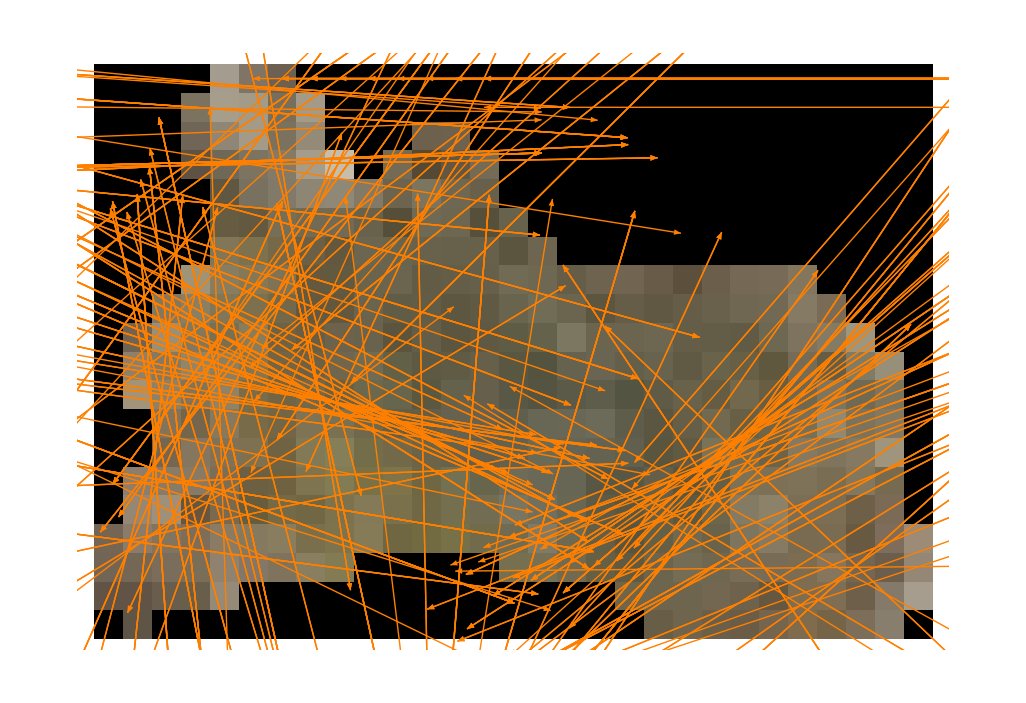

```mathematica
img=-Graphics-;
img=Image[ImageData[img] RotateLeft[DiskMatrix[300,Reverse@ImageDimensions@img],{0,3}]]
orientation=ImageData[GradientOrientationFilter[img,5]];
orientation=Image@ArcTan[Sin[orientation],-Cos[orientation]];pos=RandomChoice[ImageValuePositions[MorphologicalPerimeter[Binarize[img,{0,.5}]],1],350];
Show[img,Graphics[Table[{Orange,Arrowheads[{-.02,.02}],
o=ImageValue[orientation,p];
Arrow[p+#*{Cos[o],Sin[o]}&/@{-15,15}]},{p,pos}]]]
```

```mathematica
img=-Graphics-;
dims = ImageDimensions[img];
dirs=ImageData[GradientOrientationFilter[img,5]];
magnitudes=ImageData[GradientFilter[img,5]];
orientations = MapThread[#1{-Sin[#2],Cos[#2]}&,{magnitudes,dirs},2];
Show[img,ListVectorPlot[MapIndexed[{{#2[[2]],dims[[2]]-#2[[1]]},#1}&,orientations,{2}],VectorColorFunction->(Yellow&)]]
```

-Graphics-

```mathematica
f[x_,y_]:={-1-x^2+y,1+x-y^2};
DynamicModule[{pt={1,0}},LocatorPane[Dynamic[pt],VectorPlot[f[x,y],{x,-3,3},{y,-3,3},StreamPoints->Coarse,StreamColorFunction->Hue,Epilog->Dynamic@Inset[{pt,f@@pt},pt],PerformanceGoal->"Quality"],AutoAction->True,Appearance->Style["●",Red]]
]
```

```mathematica
ClearAll["Global'*"];img=-Graphics-;
dims = ImageDimensions[img];
dirs=ImageData[GradientOrientationFilter[img,1]];
magnitudes=ImageData[GradientFilter[img,{1,1}]];
orientations = MapThread[#1*{Sin[-#2],-Cos[#2]}&,{magnitudes,dirs},2];
(*Show[img,ListVectorPlot[MapIndexed[{{#2[[2]],dims[[2]]-#2[[1]]},#1}&,orientations,{2}],VectorColorFunction->(Green&),VectorPoints->All]]*)
Show[img,ListStreamDensityPlot[MapIndexed[{{#2[[2]],dims[[2]]-#2[[1]]},#1}&,orientations,{2}],Mesh->All]]
```

-Graphics-